```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/kevin/Documents/Projects/KevLinDev/kld-intersections/ref

## Helper methods

```mathematica
<< Bezout.m
```

```mathematica
BezoutDet = Subscript[v, i_,j_] :>xs[[i+1]] ys[[j+1]] - xs[[j+1]] ys[[i +1]]
```

v_(i_,j_):>xs⟦i+1⟧ ys⟦j+1⟧-xs⟦j+1⟧ ys⟦i+1⟧

## Define controls points of first curve

```mathematica
a1x = 150; a1y = 150
```

150

```mathematica
a2x = 183.33333333333331;a2y = 216.66666666666663
```

216.667

```mathematica
a3x = 233.33333333333337;a3y =216.66666666666663
```

216.667

```mathematica
a4x = 300;a4y =150
```

150

## Define control points of second curve

```mathematica
b1x = 100;b1y =200
```

200

```mathematica
b2x = 166.66666666666663; b2y = 133.33333333333337
```

133.333

```mathematica
b3x = 233.33333333333337; b3y = 133.33333333333337
```

133.333

```mathematica
b4x = 300;b4y =200
```

200

## Calculate Berstein coefficients for first curve

```mathematica
c13x = {a1x, a2x, a3x, a4x}.{-1, 3, -3, 1}
```

-1.13687×10^-13

```mathematica
c13y = {a1y, a2y, a3y, a4y}.{-1, 3, -3, 1}
```

0.

```mathematica
c12x = {a1x, a2x, a3x}.{3, -6, 3}
```

50.

```mathematica
c12y = {a1y, a2y, a3y}.{3, -6, 3}
```

-200.

```mathematica
c11x = {a1x, a2x}.{-3, 3}
```

100.

```mathematica
c11y = {a1y, a2y}.{-3, 3}
```

200.

```mathematica
c10x = a1x
```

150

```mathematica
c10y = a1y
```

150

## Calculate Berstein coefficients for second curve

```mathematica
c23x = {b1x, b2x, b3x, b4x}.{-1, 3, -3, 1}
```

-2.27374×10^-13

```mathematica
c23y = {b1y, b2y, b3y, b4y}.{-1, 3, -3, 1}
```

0.

```mathematica
c22x = {b1x, b2x, b3x}.{3, -6, 3}
```

3.41061×10^-13

```mathematica
c22y = {b1y, b2y, b3y}.{3, -6, 3}
```

200.

```mathematica
c21x = {b1x, b2x}.{-3, 3}
```

200.

```mathematica
c21y = {b1y, b2y}.{-3, 3}
```

-200.

```mathematica
c20x = b1x
```

100

```mathematica
c20y = b1y
```

200

## Define Berstein polynomials

```mathematica
x1 = {c10x, c11x, c12x, c13x}.{1, t, t^2, t^3}
```

150+100. t+50. t^2-1.13687×10^-13 t^3

```mathematica
y1 = {c10y, c11y, c12y, c13y}.{1, t, t^2, t^3}
```

150.+200. t-200. t^2

```mathematica
x2 = {c20x, c21x, c22x, c23x}.{1, s, s^2, s^3}
```

100+200. s+3.41061×10^-13 s^2-2.27374×10^-13 s^3

```mathematica
y2 = {c20y, c21y, c22y, c23y}.{1, s, s^2, s^3}
```

200.-200. s+200. s^2

## Set axes equal to one another, grouped by ‘t’

```mathematica
xs = CoefficientList[x2 - x1, t]
```

{-50+200. s+3.41061×10^-13 s^2-2.27374×10^-13 s^3,-100.,-50.,1.13687×10^-13}

```mathematica
ys = CoefficientList[y2 - y1, t]
```

{50.-200. s+200. s^2,-200.,200.}

```mathematica
ys = Append[ys, 0]
```

{50.-200. s+200. s^2,-200.,200.,0}

## Find determinant of Bezout matrix

```mathematica
BezoutMatrix[3] //MatrixForm
```

(v_(3,2) | v_(3,1) | v_(3,0)
v_(3,1) | v_(2,1)+v_(3,0) | v_(2,0)
v_(3,0) | v_(2,0) | v_(1,0))

```mathematica
bd = Collect[Det[BezoutMatrix[3] /. BezoutDet], s]
```

-0.0115108+0.0511591 s-0.0306954 s^2-0.0136424 s^3-0.00227374 s^4+2.06795×10^-17 s^5-5.87747×10^-32 s^6

## Plot the resulting polynomial

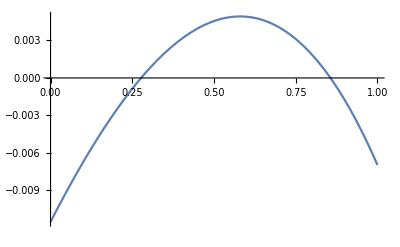

```mathematica
Plot[bd,{s,0,1}]
```

## Compare to the polynomial I got in Javascript

```mathematica
mybd = -0.011510792319313606 +0.051159076974727116*s - 0.030695446184836248*s^2-0.013642420526593955*s^3-0.0022737367544323115*s^4 + 2.067951531382581 × 10^-17*s^5- 5.877471754111428×10^-32*s^6
```

-0.0115108+0.0511591 s-0.0306954 s^2-0.0136424 s^3-0.00227374 s^4+2.06795×10^-17 s^5-5.87747×10^-32 s^6

```mathematica
Plot[mybd, {s, 0, 1}]
```

-Graphics-

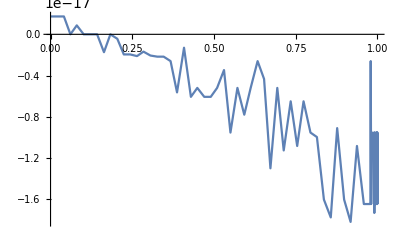

```mathematica
Plot[mybd-bd,{s, 0, 1}]
```

## Find roots in ‘s’ for both polynomials

```mathematica
bdroots = Solve[bd == 0, s, Reals]
```

{{s→0.276945},{s→0.856327}}

```mathematica
Solve[mybd == 0, s, Reals]
```

{{s→0.276945},{s→0.856327}}

```mathematica
mybdroots = {{s-> 0.27693915367126465}, {s -> 0.8563182353973389}}
```

{{s→0.276939},{s→0.856318}}

## Apply roots

#### Mathematica’s roots

```mathematica
rx1 = (x2 - x1) /. bdroots[[1]]
```

5.38897-100. t-50. t^2+1.13687×10^-13 t^3

```mathematica
rx2 = (x2 - x1) /. bdroots[[2]]
```

121.265-100. t-50. t^2+1.13687×10^-13 t^3

```mathematica
ry1 = (y2 - y1) /. bdroots[[1]]
```

9.95072-200. t+200. t^2

```mathematica
ry2 = (y2 - y1) /. bdroots[[2]]
```

25.3937-200. t+200. t^2

#### My roots from Javascript

```mathematica
mrx1 = (x2 - x1) /. mybdroots[[1]]
```

5.38783-100. t-50. t^2+1.13687×10^-13 t^3

```mathematica
mrx2 = (x2 - x1) /. mybdroots[[2]]
```

121.264-100. t-50. t^2+1.13687×10^-13 t^3

```mathematica
mry1 = (y2 - y1) /. mybdroots[[1]]
```

9.95123-200. t+200. t^2

```mathematica
mry2 = (y2 - y1) /. mybdroots[[2]]
```

25.3925-200. t+200. t^2

## Find roots in ‘t’

#### Mathematica

```mathematica
Solve[rx1 == 0, t]
```

{{t→-2.05251},{t→0.052511},{t→4.39805×10^14}}

```mathematica
Solve[rx2 == 0, t]
```

{{t→-2.85076},{t→0.850758},{t→4.39805×10^14}}

```mathematica
Solve[ry1 == 0, t]
```

{{t→0.052511},{t→0.947489}}

```mathematica
Solve[ry2 == 0, t]
```

{{t→0.149242},{t→0.850758}}

#### Mine

```mathematica
Solve[mrx1 == 0, t]
```

{{t→-2.0525},{t→0.0525002},{t→4.39805×10^14}}

```mathematica
Solve[mrx2 == 0, t]
```

{{t→-2.85075},{t→0.850749},{t→4.39805×10^14}}

```mathematica
Solve[mry1 == 0, t]
```

{{t→0.0525138},{t→0.947486}}

```mathematica
Solve[mry2 == 0, t]
```

{{t→0.149233},{t→0.850767}}